```mathematica
rota[t_,n_,n1_,n2_]:=Module[{mat},mat=IdentityMatrix[n];mat[[n1]][[n1]]=Cos[t];mat[[n2]][[n2]]=Cos[t];mat[[n1]][[n2]]=-Sin[t];mat[[n2]][[n1]]=Sin[t];mat]
```

```mathematica
rota[t0102,2,1,2]//MatrixForm
```

(Cos[t0102] | -Sin[t0102]
Sin[t0102] | Cos[t0102])

```mathematica
r01[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
mat[[;;,1]]]
```

```mathematica
r01[t,2]//MatrixForm
```

(Cos[t[1,1]]
Sin[t[1,1]])

```mathematica
r01[t,3]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]]
Cos[t[1,2]] Sin[t[1,1]]
Sin[t[1,2]])

```mathematica
r01[t,4]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]]
Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]]
Cos[t[1,3]] Sin[t[1,2]]
Sin[t[1,3]])

```mathematica
NMinimize[Max[Abs[r01[t,2][[1]]],Abs[r01[t,2][[2]]]],{t[1,1]}]
```

{0.707107,{t[1,1]→-0.785398}}

```mathematica
NMinimize[Max[Abs[r01[t,3][[1]]],Abs[r01[t,3][[2]]],Abs[r01[t,3][[3]]]],{t[1,1],t[1,2]}]
```

{0.57735,{t[1,1]→0.785398,t[1,2]→0.61548}}

```mathematica
NMinimize[Max[Abs[r01[t,4][[1]]],Abs[r01[t,4][[2]]],Abs[r01[t,4][[3]]],Abs[r01[t,4][[4]]]],{t[1,1],t[1,2],t[1,3]}]
```

{0.500998,{t[1,1]→0.781719,t[1,2]→0.617118,t[1,3]→-0.524752}}

```mathematica
NMinimize[Max[Abs[r01[t,5][[1]]],Abs[r01[t,5][[2]]],Abs[r01[t,5][[3]]],Abs[r01[t,5][[4]]],Abs[r01[t,5][[5]]]],{t[1,1],t[1,2],t[1,3],t[1,4]}]
```

{0.476507,{t[1,1]→-0.785406,t[1,2]→0.615434,t[1,3]→0.351911,t[1,4]→-0.496655}}

```mathematica
NSolve[{r01[t,2][[1]]==r01[t,2][[2]],
0<=t[1,1]≤Pi/2},{t[1,1]}]
```

{{t[1,1]→0.785398}}

```mathematica
1/r01[t,2][[1]]^2/.{t[1,1]->0.7853981633974483}
```

2.

```mathematica
NSolve[{r01[t,3][[1]]==r01[t,3][[2]],
r01[t,3][[2]]==r01[t,3][[3]],
0<=t[1,1]≤Pi/2,
0≤t[1,2]≤Pi/2},{t[1,1],t[1,2]}]
```

{{t[1,1]→0.785398,t[1,2]→0.61548}}

```mathematica
1/r01[t,3][[1]]^2/.{t[1,1]->0.7853981633974483,t[1,2]->0.6154797086703869}
```

3.

```mathematica
NSolve[{r01[t,4][[1]]==r01[t,4][[2]],
r01[t,4][[2]]==r01[t,4][[3]],
r01[t,4][[3]]==r01[t,4][[4]]},{t[1,1],t[1,2],t[1,3]}][[1]]
```

{t[1,1]→ConditionalExpression[1. (-2.35619+6.28319 C[1]),C[1]∈ℤ],t[1,2]→ConditionalExpression[1. (-0.61548+6.28319 C[2]),C[2]∈ℤ],t[1,3]→ConditionalExpression[1. (-0.523599+6.28319 C[3]),C[3]∈ℤ]}

```mathematica
N[1/r01[t,4][[1]]^2/.{t[1,1]->-2.356194490192345,t[1,2]->-0.6154797086703873,t[1,3]->-0.5235987755982988}]
```

4.

```mathematica
NSolve[{
r01[t,5][[1]]==r01[t,5][[2]],
r01[t,5][[2]]==r01[t,5][[3]],
r01[t,5][[3]]==r01[t,5][[4]],
r01[t,5][[4]]==r01[t,5][[5]]
},{t[1,1],t[1,2],t[1,3],t[1,4]}][[1]]
```

{t[1,1]→ConditionalExpression[1. (-2.35619+6.28319 C[1]),C[1]∈ℤ],t[1,2]→ConditionalExpression[1. (-0.61548+6.28319 C[2]),C[2]∈ℤ],t[1,3]→ConditionalExpression[1. (-0.523599+6.28319 C[3]),C[3]∈ℤ],t[1,4]→ConditionalExpression[1. (-0.463648+6.28319 C[4]),C[4]∈ℤ]}

```mathematica
N[1/r01[t,5][[1]]^2/.{t[1,1]->-2.356194490192345,t[1,2]->-0.6154797086703873,t[1,3]->-0.5235987755982988,t[1,4]->-0.46364760900080615}]
```

5.

```mathematica
FindRoot[Evaluate[r01[t,2][[1]]==r01[t,2][[2]]/.t[1,1]->t0101],{t0101,Pi/4}]/.t0101->t[1,1]
```

{t[1,1]→0.785398}

```mathematica
FindRoot[Evaluate[{r01[t,3][[1]]==r01[t,3][[2]],
r01[t,3][[2]]==r01[t,3][[3]]}/.{t[1,1]->t0101,t[1,2]->t0102}],{{t0101,Pi/4},{t0102,Pi/4}}]/.{t0101->t[1,1],t0102->t[1,2]}
```

{t[1,1]→0.785398,t[1,2]→0.61548}

```mathematica
FindRoot[Evaluate[{r01[t,4][[1]]==r01[t,4][[2]],
r01[t,4][[2]]==r01[t,4][[3]],
r01[t,4][[3]]==r01[t,4][[4]]}/.{t[1,1]->t0101,t[1,2]->t0102,t[1,3]->t0103}],{t0101,Pi/4},{t0102,Pi/4},{t0103,Pi/4}]/.{t0101->t[1,1],t0102->t[1,2],t0103->t[1,3]}
```

{t[1,1]→0.785398,t[1,2]→0.61548,t[1,3]→0.523599}

```mathematica
r02[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
Do[mat=mat.rota[t[2,i-1],n,2,i],{i,3,n}];
mat[[;;,1;;2]]]
```

```mathematica
r02[t,3]/.t[1,2]->0//MatrixForm
```

(Cos[t[1,1]] | -Cos[t[2,2]] Sin[t[1,1]]
Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,2]]
0 | Sin[t[2,2]])

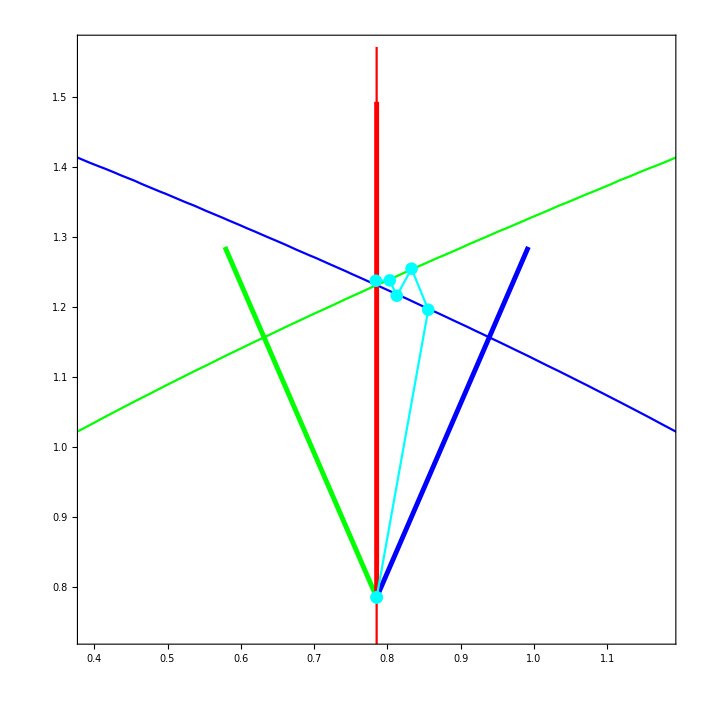

```mathematica
Show[ContourPlot[{Abs[Cos[t[1,1]]]+Abs[-Cos[t[2,2]] Sin[t[1,1]]]==Abs[Sin[t[1,1]]]+Abs[Cos[t[1,1]] Cos[t[2,2]]],Abs[Sin[t[1,1]]]+Abs[Cos[t[1,1]] Cos[t[2,2]]]==Abs[Sin[t[2,2]]],Abs[Sin[t[2,2]]]==Abs[Cos[t[1,1]]]+Abs[-Cos[t[2,2]] Sin[t[1,1]]]},{t[1,1],0,Pi/2},{t[2,2],0,Pi/2},PlotRange->{{Pi/8,3Pi/8},{Pi/4-0.05,Pi/2}},PlotPoints->20,ContourStyle->{Red,Green,Blue}],ListPlot[{{t[1,1],t[2,2]},{t[1,1]+0.20710,t[2,2]+0.5}}/.{t[1,1]->Pi/4,t[2,2]->Pi/4},Joined->True,PlotStyle->{Blue,Thickness[0.005]}],ListPlot[{{t[1,1],t[2,2]},{t[1,1]-0.20710,t[2,2]+0.5}}/.{t[1,1]->Pi/4,t[2,2]->Pi/4},Joined->True,PlotStyle->{Green,Thickness[0.005]}],ListPlot[{{t[1,1],t[2,2]},{t[1,1]+0.0,t[2,2]+0.70710}}/.{t[1,1]->Pi/4,t[2,2]->Pi/4},Joined->True,PlotStyle->{Red,Thickness[0.005]}],ListPlot[{
{0.7853981633974483,0.7853981633974483},
{0.7853981633974483,0.7853981633974483},
{0.8558144690008744,1.1958144690008745},
{0.8330719371704102,1.2543927246046769},
{0.8129046028695386,1.2158448198408784},
{0.8033351643435257,1.2376707327877448},
{0.7843028662136552,1.2371913142901048}
},Mesh->All,Joined->True,PlotStyle->{Cyan}]]
```

```mathematica
{Abs[Cos[t[1,1]] Cos[t[1,2]]]+Abs[-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]]==Abs[Cos[t[1,2]] Sin[t[1,1]]]+Abs[Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]],
Abs[Cos[t[1,2]] Sin[t[1,1]]]+Abs[Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]]==Abs[Sin[t[1,2]]]+Abs[Cos[t[1,2]] Sin[t[2,2]]]}/.t[1,2]->0//MatrixForm
```

(Abs[Cos[t[1,1]]]+Abs[Cos[t[2,2]] Sin[t[1,1]]]==Abs[Cos[t[1,1]] Cos[t[2,2]]]+Abs[Sin[t[1,1]]]
Abs[Cos[t[1,1]] Cos[t[2,2]]]+Abs[Sin[t[1,1]]]==Abs[Sin[t[2,2]]])

```mathematica
FindRoot[{Abs[Cos[t[1,1]] Cos[t[1,2]]]+Abs[-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]]==Abs[Cos[t[1,2]] Sin[t[1,1]]]+Abs[Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]],
Abs[Cos[t[1,2]] Sin[t[1,1]]]+Abs[Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]]==Abs[Sin[t[1,2]]]+Abs[Cos[t[1,2]] Sin[t[2,2]]]}/.t[1,2]->0,{{t[1,1],Pi/4},{t[2,2],Pi/4}}]
```

{t[1,1]→0.785398,t[2,2]→1.23096}

```mathematica
r02[t,3]/.{t[1,1]->0.7853981633974484,t[2,2]->1.2309594173407743,t[1,2]->0}//MatrixForm
```

(0.707107 | -0.235702
0.707107 | 0.235702
0 | 0.942809)

```mathematica
r02[t,5]/.{t[1,4]->0,t[1,3]->0,t[1,2]->0}//MatrixForm
```

(Cos[t[1,1]] | -Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Sin[t[1,1]]
Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]]
0 | Cos[t[2,3]] Cos[t[2,4]] Sin[t[2,2]]
0 | Cos[t[2,4]] Sin[t[2,3]]
0 | Sin[t[2,4]])

```mathematica
r02[t,5]/.{t[1,4]->0,t[1,3]->0,t[2,2]->0}//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] | -Cos[t[2,3]] Cos[t[2,4]] Sin[t[1,1]]
Cos[t[1,2]] Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,3]] Cos[t[2,4]]
Sin[t[1,2]] | 0
0 | Cos[t[2,4]] Sin[t[2,3]]
0 | Sin[t[2,4]])

```mathematica
r02[t,5]/.{t[1,4]->0,t[1,3]->0,t[2,2]->0,t[1,1]->0.7853981633974536,t[1,2]->0.7559694104239032,t[2,3]->1.2309594173407803,t[2,4]->0.7559694104239093}//MatrixForm
```

(0.514496 | -0.171499
0.514496 | 0.171499
0.685994 | 0.
0 | 0.685994
0 | 0.685994)

```mathematica
g0211 =r02[t,11]/.{t[1,10]->0,t[1,9]->0,t[1,8]->0,t[1,7]->0,t[1,6]->0,t[2,5]->0,t[2,4]->0,t[2,3]->0,t[2,2]->0};
g0211//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] | -Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Cos[t[2,10]] Sin[t[1,1]]
Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Cos[t[2,10]]
Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] | 0
Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] | 0
Cos[t[1,5]] Sin[t[1,4]] | 0
Sin[t[1,5]] | 0
0 | Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Cos[t[2,10]] Sin[t[2,6]]
0 | Cos[t[2,8]] Cos[t[2,9]] Cos[t[2,10]] Sin[t[2,7]]
0 | Cos[t[2,9]] Cos[t[2,10]] Sin[t[2,8]]
0 | Cos[t[2,10]] Sin[t[2,9]]
0 | Sin[t[2,10]])

```mathematica
a0211=FullSimplify[1/Sqrt[5+1/8]]
```

2 √(2/41)

```mathematica
N[a0211]
```

0.441726

```mathematica
FullSimplify[ArcSin[a0211]]
```

ArcSin[2 √(2/41)]

```mathematica
FullSimplify[ArcSin[a0211/Cos[ArcSin[a0211]]]]
```

ArcTan[(2 √2)/5]

```mathematica
FullSimplify[ArcSin[a0211/Sqrt[25/41]]]
```

ArcSin[(2 √2)/5]

```mathematica
FullSimplify[ArcSin[a0211/Sqrt[17/41]]]
```

ArcTan[(2 √2)/3]

```mathematica
FullSimplify[ArcSin[a0211/Sqrt[9/41]]]
```

ArcTan[2 √2]

```mathematica
Solve[Sin[x]Sqrt[9/41]+Cos[x]Sqrt[1/41]==a0211,x]
```

{{x→ConditionalExpression[π/4+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π-ArcTan[7]+2 π C[1],C[1]∈ℤ]}}

```mathematica
g0211/.{t[1,5]->ArcSin[2 √(2/41)],t[2,10]->ArcSin[2 √(2/41)],t[1,4]->ArcTan[(2 √2)/5],t[2,9]->ArcTan[(2 √2)/5],t[1,3]->ArcSin[(2 √2)/5],t[2,8]->ArcSin[(2 √2)/5],t[1,2]->ArcTan[(2 √2)/3],t[2,7]->ArcTan[(2 √2)/3],t[2,6]->ArcTan[2 √2],t[1,1]->Pi/4}//MatrixForm
```

(3/(√82) | -1/(√82)
3/(√82) | 1/(√82)
2 √(2/41) | 0
2 √(2/41) | 0
2 √(2/41) | 0
2 √(2/41) | 0
0 | 2 √(2/41)
0 | 2 √(2/41)
0 | 2 √(2/41)
0 | 2 √(2/41)
0 | 2 √(2/41))

```mathematica
N[g0211/.{t[1,5]->ArcSin[2 √(2/41)],t[2,10]->ArcSin[2 √(2/41)],t[1,4]->ArcTan[(2 √2)/5],t[2,9]->ArcTan[(2 √2)/5],t[1,3]->ArcSin[(2 √2)/5],t[2,8]->ArcSin[(2 √2)/5],t[1,2]->ArcTan[(2 √2)/3],t[2,7]->ArcTan[(2 √2)/3],t[2,6]->ArcTan[2 √2],t[1,1]->Pi/4}//MatrixForm]
```

(0.331295 | -0.110432
0.331295 | 0.110432
0.441726 | 0.
0.441726 | 0.
0.441726 | 0.
0.441726 | 0.
0. | 0.441726
0. | 0.441726
0. | 0.441726
0. | 0.441726
0. | 0.441726)

```mathematica
N[Join[Table[t[1,i],{i,1,5}],Table[t[2,i],{i,6,10}]]/.{t[1,5]->ArcSin[2 √(2/41)],t[2,10]->ArcSin[2 √(2/41)],t[1,4]->ArcTan[(2 √2)/5],t[2,9]->ArcTan[(2 √2)/5],t[1,3]->ArcSin[(2 √2)/5],t[2,8]->ArcSin[(2 √2)/5],t[1,2]->ArcTan[(2 √2)/3],t[2,7]->ArcTan[(2 √2)/3],t[2,6]->ArcTan[2 √2],t[1,1]->Pi/4}]
```

{0.785398,0.755969,0.601264,0.514806,0.457522,1.23096,0.755969,0.601264,0.514806,0.457522}

```mathematica
g0211/.{t[1,1]->0.7853981633974308,t[1,2]->0.6809418794626028,t[1,3]->0.5618467217547932,t[1,4]->0.48950301392479906,t[1,5]->0.43951430641381617,t[2,6]->1.3927213597826644,t[2,7]->0.7774285709856019,t[2,8]->0.6116978074567081,t[2,9]->0.5212766475202373,t[2,10]->0.5463265007726131}//MatrixForm
```

(0.371348 | -0.0541517
0.371348 | 0.0541517
0.4255 | 0
0.4255 | 0
0.4255 | 0
0.4255 | 0
0 | 0.4255
0 | 0.4255
0 | 0.4255
0 | 0.4255
0 | 0.519552)

```mathematica
r03[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
Do[mat=mat.rota[t[2,i-1],n,2,i],{i,3,n}];
Do[mat=mat.rota[t[3,i-1],n,3,i],{i,4,n}];
mat[[;;,1;;3]]]
```

```mathematica
r03[t,4]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] | Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[3,3]] (-Cos[t[1,1]] Cos[t[2,2]] Sin[t[1,2]]+Sin[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]-(-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]]
Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] | Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[3,3]] (-Cos[t[2,2]] Sin[t[1,1]] Sin[t[1,2]]-Cos[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,1]] Sin[t[1,3]]-(Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[1,2]] Cos[t[2,2]] Cos[t[3,3]]+(-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,2]] Sin[t[2,3]]) Sin[t[3,3]]
Sin[t[1,3]] | Cos[t[1,3]] Sin[t[2,3]] | Cos[t[1,3]] Cos[t[2,3]] Sin[t[3,3]])

```mathematica
(r03[t,4]/.{t[1,3]->0,t[1,2]->0,t[2,3]->0})//MatrixForm
```

(Cos[t[1,1]] | -Cos[t[2,2]] Sin[t[1,1]] | Cos[t[3,3]] Sin[t[1,1]] Sin[t[2,2]]
Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,2]] | -Cos[t[1,1]] Cos[t[3,3]] Sin[t[2,2]]
0 | Sin[t[2,2]] | Cos[t[2,2]] Cos[t[3,3]]
0 | 0 | Sin[t[3,3]])

```mathematica
r03[t,7]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] | Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]] | Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (Cos[t[3,3]] (-Cos[t[1,1]] Cos[t[2,2]] Sin[t[1,2]]+Sin[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]-(-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]
Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,1]] | Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,1]] Sin[t[1,6]] Sin[t[2,6]] | Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (Cos[t[3,3]] (-Cos[t[2,2]] Sin[t[1,1]] Sin[t[1,2]]-Cos[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,1]] Sin[t[1,3]]-(Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,1]] Sin[t[1,4]]-(Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,1]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,1]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]
Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,2]] | Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]] | Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (Cos[t[1,2]] Cos[t[2,2]] Cos[t[3,3]]+(-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,2]] Sin[t[2,3]]) Sin[t[3,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,2]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,2]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]
Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] | Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]] | Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]] Sin[t[3,3]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,3]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]
Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] | Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]] | Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]+(-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,4]] Sin[t[1,6]]-(Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]]
Cos[t[1,6]] Sin[t[1,5]] | Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]] | Cos[t[1,5]] Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]+(-Cos[t[2,6]] Sin[t[1,5]] Sin[t[1,6]]-Cos[t[1,5]] Sin[t[2,5]] Sin[t[2,6]]) Sin[t[3,6]]
Sin[t[1,6]] | Cos[t[1,6]] Sin[t[2,6]] | Cos[t[1,6]] Cos[t[2,6]] Sin[t[3,6]])

```mathematica
(r03[t,7]/.{t[1,6]->0,t[1,5]->0,t[1,4]->0,t[1,3]->0,t[2,2]->0,t[2,6]->0,t[2,5]->0,t[3,4]->0,t[3,3]->0})//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] | -Cos[t[2,3]] Cos[t[2,4]] Sin[t[1,1]] | -Cos[t[1,1]] Cos[t[3,5]] Cos[t[3,6]] Sin[t[1,2]]
Cos[t[1,2]] Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,3]] Cos[t[2,4]] | -Cos[t[3,5]] Cos[t[3,6]] Sin[t[1,1]] Sin[t[1,2]]
Sin[t[1,2]] | 0 | Cos[t[1,2]] Cos[t[3,5]] Cos[t[3,6]]
0 | Cos[t[2,4]] Sin[t[2,3]] | 0
0 | Sin[t[2,4]] | 0
0 | 0 | Cos[t[3,6]] Sin[t[3,5]]
0 | 0 | Sin[t[3,6]])

```mathematica
r03[t,10]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
r03[t,10]/.{t[1,9]->0,t[1,8]->0,t[1,7]->0,t[1,6]->0,t[1,5]->0,t[1,4]->0,t[2,3]->0,t[2,2]->0,t[2,9]->0,t[2,8]->0,t[2,7]->0,t[3,6]->0,t[3,5]->0,t[3,4]->0,t[3,3]->0}//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] | -Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Sin[t[1,1]] | -Cos[t[1,1]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[1,2]]
Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] | -Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[1,1]] Sin[t[1,2]]
Cos[t[1,3]] Sin[t[1,2]] | 0 | Cos[t[1,2]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]
Sin[t[1,3]] | 0 | 0
0 | Cos[t[2,5]] Cos[t[2,6]] Sin[t[2,4]] | 0
0 | Cos[t[2,6]] Sin[t[2,5]] | 0
0 | Sin[t[2,6]] | 0
0 | 0 | Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,7]]
0 | 0 | Cos[t[3,9]] Sin[t[3,8]]
0 | 0 | Sin[t[3,9]])

```mathematica
r03[t,10]/.{t[1,9]->0,t[1,8]->0,t[1,7]->0,t[1,6]->0,t[1,5]->0,t[1,4]->0,t[2,3]->0,t[2,2]->0,t[2,9]->0,t[2,8]->0,t[2,7]->0,t[3,6]->0,t[3,5]->0,t[3,4]->0,t[3,3]->0,t[1,1]->0.7853981633974482,t[1,2]->2.49240477484607,t[1,3]->2.5296498515191974,t[2,4]->1.3985200823453316,t[2,5]->0.7779416685265444,t[2,6]->2.5296498515191983,t[3,7]->1.7430725712444317,t[3,8]->0.7779416685265468,t[3,9]->0.6119428020705963}//MatrixForm
```

(0.46105 | 0.0706799 | 0.0427288
0.46105 | -0.0706799 | 0.0427288
-0.494836 | 0. | 0.0796228
0.574459 | 0. | 0.
0 | -0.574459 | 0.
0 | -0.574459 | 0.
0 | 0.574459 | 0.
0 | 0 | 0.574459
0 | 0 | 0.574459
0 | 0 | 0.574459)

```mathematica
0.4610501270261963+0.07067987506422467+0.04272878973652186
```

0.574459

```mathematica
0.4948359902341234+0.07962280159281968
```

0.574459

```mathematica
r03[t,10]/.{t[1,9]->0,t[1,8]->0,t[1,7]->0,t[1,6]->0,t[1,5]->0,t[1,4]->0,t[2,3]->0,t[2,2]->0,t[2,9]->0,t[2,8]->0,t[2,7]->0,t[3,6]->0,t[3,5]->0,t[3,4]->0}//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] | -Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Sin[t[1,1]] | Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] (-Cos[t[1,1]] Cos[t[3,3]] Sin[t[1,2]]-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[3,3]])
Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] | Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] (-Cos[t[3,3]] Sin[t[1,1]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[3,3]])
Cos[t[1,3]] Sin[t[1,2]] | 0 | Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] (Cos[t[1,2]] Cos[t[3,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[3,3]])
Sin[t[1,3]] | 0 | Cos[t[1,3]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]
0 | Cos[t[2,5]] Cos[t[2,6]] Sin[t[2,4]] | 0
0 | Cos[t[2,6]] Sin[t[2,5]] | 0
0 | Sin[t[2,6]] | 0
0 | 0 | Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,7]]
0 | 0 | Cos[t[3,9]] Sin[t[3,8]]
0 | 0 | Sin[t[3,9]])

```mathematica
r03[t,10]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
c1roots=FindRoot[{
Sin[t[1,9]] == 0,
Cos[t[1,9]] Sin[t[1,8]]==0,
Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,7]]==0,
Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,6]]==0,
Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,5]]==0,
Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,4]]==0,
Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,3]]==0.5,
Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,2]]==0.5,
Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,1]]==0.5
},{{t[1,1],0},{t[1,2],0},{t[1,3],0},{t[1,4],0},{t[1,5],0},{t[1,6],0},{t[1,7],0},{t[1,8],0},{t[1,9],0}}]
```

{t[1,1]→0.785398,t[1,2]→0.61548,t[1,3]→0.523599,t[1,4]→0.,t[1,5]→0.,t[1,6]→0.,t[1,7]→0.,t[1,8]→0.,t[1,9]→0.}

```mathematica
Expand[(r03[t,10]/.c1roots)]//MatrixForm
```

(0.5 | 0.-0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]]-0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,2]]-0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,3]] | 0.-0.408248 Cos[t[2,2]] Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]+0.707107 Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]]-0.288675 Cos[t[2,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]+0.707107 Cos[t[2,2]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[3,3]]+0.408248 Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,3]] Sin[t[3,3]]+0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,4]] Sin[t[3,4]]+0.408248 Cos[t[2,3]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,4]] Sin[t[3,4]]+0.288675 Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,4]] Sin[t[3,4]]+0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,5]] Sin[t[3,5]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,5]] Sin[t[3,5]]+0.288675 Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,5]] Sin[t[3,5]]+0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,6]] Sin[t[3,6]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,6]] Sin[t[3,6]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,6]] Sin[t[3,6]]+0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,7]] Sin[t[3,7]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,7]] Sin[t[3,7]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,7]] Sin[t[3,7]]+0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,8]] Sin[t[3,8]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,8]] Sin[t[3,8]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,8]] Sin[t[3,8]]+0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,9]] Sin[t[3,9]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,2]] Sin[t[2,9]] Sin[t[3,9]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,3]] Sin[t[2,9]] Sin[t[3,9]]
0.5 | 0.+0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]]-0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,2]]-0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,3]] | 0.-0.408248 Cos[t[2,2]] Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]-0.707107 Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]]-0.288675 Cos[t[2,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]-0.707107 Cos[t[2,2]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[3,3]]+0.408248 Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,3]] Sin[t[3,3]]-0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,4]] Sin[t[3,4]]+0.408248 Cos[t[2,3]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,4]] Sin[t[3,4]]+0.288675 Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,4]] Sin[t[3,4]]-0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,5]] Sin[t[3,5]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,5]] Sin[t[3,5]]+0.288675 Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,5]] Sin[t[3,5]]-0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,6]] Sin[t[3,6]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,6]] Sin[t[3,6]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,6]] Sin[t[3,6]]-0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,7]] Sin[t[3,7]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,7]] Sin[t[3,7]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,7]] Sin[t[3,7]]-0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,8]] Sin[t[3,8]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,8]] Sin[t[3,8]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,8]] Sin[t[3,8]]-0.707107 Cos[t[2,2]] Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,9]] Sin[t[3,9]]+0.408248 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,2]] Sin[t[2,9]] Sin[t[3,9]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,3]] Sin[t[2,9]] Sin[t[3,9]]
0.5 | 0.+0.816497 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,2]]-0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,3]] | 0.+0.816497 Cos[t[2,2]] Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]-0.288675 Cos[t[2,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]-0.816497 Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,3]] Sin[t[3,3]]-0.816497 Cos[t[2,3]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,4]] Sin[t[3,4]]+0.288675 Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,4]] Sin[t[3,4]]-0.816497 Cos[t[2,3]] Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,5]] Sin[t[3,5]]+0.288675 Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,5]] Sin[t[3,5]]-0.816497 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,6]] Sin[t[3,6]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,6]] Sin[t[3,6]]-0.816497 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,7]] Sin[t[3,7]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,7]] Sin[t[3,7]]-0.816497 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,2]] Sin[t[2,8]] Sin[t[3,8]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,8]] Sin[t[3,8]]-0.816497 Cos[t[2,3]] Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,2]] Sin[t[2,9]] Sin[t[3,9]]+0.288675 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,3]] Sin[t[2,9]] Sin[t[3,9]]
0.5 | 0.+0.866025 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,3]] | 0.+0.866025 Cos[t[2,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]-0.866025 Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,4]] Sin[t[3,4]]-0.866025 Cos[t[2,4]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,5]] Sin[t[3,5]]-0.866025 Cos[t[2,4]] Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,6]] Sin[t[3,6]]-0.866025 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,7]] Sin[t[3,7]]-0.866025 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,3]] Sin[t[2,8]] Sin[t[3,8]]-0.866025 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,3]] Sin[t[2,9]] Sin[t[3,9]]
0. | 0.+1. Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,4]] | 0.+1. Cos[t[2,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,4]]-1. Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,4]] Sin[t[2,5]] Sin[t[3,5]]-1. Cos[t[2,5]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,4]] Sin[t[2,6]] Sin[t[3,6]]-1. Cos[t[2,5]] Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,4]] Sin[t[2,7]] Sin[t[3,7]]-1. Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,4]] Sin[t[2,8]] Sin[t[3,8]]-1. Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,4]] Sin[t[2,9]] Sin[t[3,9]]
0. | 0.+1. Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,5]] | 0.+1. Cos[t[2,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,5]]-1. Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,5]] Sin[t[2,6]] Sin[t[3,6]]-1. Cos[t[2,6]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,5]] Sin[t[2,7]] Sin[t[3,7]]-1. Cos[t[2,6]] Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,5]] Sin[t[2,8]] Sin[t[3,8]]-1. Cos[t[2,6]] Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,5]] Sin[t[2,9]] Sin[t[3,9]]
0. | 0.+1. Cos[t[2,7]] Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,6]] | 0.+1. Cos[t[2,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,6]]-1. Cos[t[3,8]] Cos[t[3,9]] Sin[t[2,6]] Sin[t[2,7]] Sin[t[3,7]]-1. Cos[t[2,7]] Cos[t[3,9]] Sin[t[2,6]] Sin[t[2,8]] Sin[t[3,8]]-1. Cos[t[2,7]] Cos[t[2,8]] Sin[t[2,6]] Sin[t[2,9]] Sin[t[3,9]]
0. | 0.+1. Cos[t[2,8]] Cos[t[2,9]] Sin[t[2,7]] | 0.+1. Cos[t[2,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,7]]-1. Cos[t[3,9]] Sin[t[2,7]] Sin[t[2,8]] Sin[t[3,8]]-1. Cos[t[2,8]] Sin[t[2,7]] Sin[t[2,9]] Sin[t[3,9]]
0. | 0.+1. Cos[t[2,9]] Sin[t[2,8]] | 0.+1. Cos[t[2,8]] Cos[t[3,9]] Sin[t[3,8]]-1. Sin[t[2,8]] Sin[t[2,9]] Sin[t[3,9]]
0. | 1. Sin[t[2,9]] | 1. Cos[t[2,9]] Sin[t[3,9]])

```mathematica
c2roots=FindRoot[{
Cos[t[1,9]] Sin[t[2,9]]==0,
Cos[t[1,8]] Cos[t[2,9]] Sin[t[2,8]]-Sin[t[1,8]] Sin[t[1,9]] Sin[t[2,9]]==0,
Cos[t[2,9]] (Cos[t[1,7]] Cos[t[2,8]] Sin[t[2,7]]-Sin[t[1,7]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,8]] Sin[t[1,7]] Sin[t[1,9]] Sin[t[2,9]]==0,
Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,7]] Sin[t[1,6]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,6]] Sin[t[1,9]] Sin[t[2,9]]==0.574166,
Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,5]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,5]] Sin[t[1,9]] Sin[t[2,9]]==0.574166,
Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,4]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,4]] Sin[t[1,9]] Sin[t[2,9]]==0.574166,
Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,3]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,3]] Sin[t[1,9]] Sin[t[2,9]]==0,
Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,2]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,2]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,2]] Sin[t[1,9]] Sin[t[2,9]]==0
}/.c1roots,
{{t[2,9],0},{t[2,8],0},{t[2,7],0},{t[2,6],0},{t[2,5],0},{t[2,4],0},{t[2,3],0},{t[2,2],0}}]
```

{t[2,9]→0.,t[2,8]→0.,t[2,7]→0.,t[2,6]→0.611585,t[2,5]→0.777193,t[2,4]→1.39012,t[2,3]→0.,t[2,2]→0.}

```mathematica
Expand[(r03[t,10]/.Join[c1roots,c2roots])]//MatrixForm
```

(0.5 | -0.0741627 | 0.-0.408248 Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]-0.288675 Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]+0.695597 Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,4]]+0.0891072 Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,5]]+0.0520089 Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,6]]
0.5 | 0.0741627 | 0.-0.408248 Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]-0.288675 Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]-0.695597 Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,4]]-0.0891072 Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,5]]-0.0520089 Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,6]]
0.5 | 0. | 0.+0.816497 Cos[t[3,3]] Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]-0.288675 Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]
0.5 | 0. | 0.+0.866025 Cos[t[3,4]] Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,3]]
0. | 0.574166 | 0.+0.179695 Cos[t[3,5]] Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,4]]-0.689866 Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,5]]-0.402652 Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,6]]
0. | 0.574166 | 0.+0.712885 Cos[t[3,6]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,5]]-0.402652 Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,6]]
0. | 0.574166 | 0.+0.818739 Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,6]]
0. | 0. | 0.+1. Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,7]]
0. | 0. | 0.+1. Cos[t[3,9]] Sin[t[3,8]]
0. | 0. | 1. Sin[t[3,9]])

```mathematica
c3roots=FindRoot[{
Cos[t[1,9]] Cos[t[2,9]] Sin[t[3,9]]==0.574166,
Cos[t[1,8]] Cos[t[2,8]] Cos[t[3,9]] Sin[t[3,8]]+(-Cos[t[2,9]] Sin[t[1,8]] Sin[t[1,9]]-Cos[t[1,8]] Sin[t[2,8]] Sin[t[2,9]]) Sin[t[3,9]]==0.574166,Cos[t[3,9]] (Cos[t[1,7]] Cos[t[2,7]] Cos[t[3,8]] Sin[t[3,7]]+(-Cos[t[2,8]] Sin[t[1,7]] Sin[t[1,8]]-Cos[t[1,7]] Sin[t[2,7]] Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,7]] Sin[t[1,9]]-(Cos[t[1,7]] Cos[t[2,8]] Sin[t[2,7]]-Sin[t[1,7]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0.574166,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[1,6]] Cos[t[2,6]] Cos[t[3,7]] Sin[t[3,6]]+(-Cos[t[2,7]] Sin[t[1,6]] Sin[t[1,7]]-Cos[t[1,6]] Sin[t[2,6]] Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,6]] Sin[t[1,8]]-(Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,6]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,7]] Sin[t[1,6]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[1,5]] Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]+(-Cos[t[2,6]] Sin[t[1,5]] Sin[t[1,6]]-Cos[t[1,5]] Sin[t[2,5]] Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,5]] Sin[t[1,7]]-(Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,5]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,5]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,5]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]+(-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,4]] Sin[t[1,6]]-(Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,4]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,4]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,4]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,4]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]] Sin[t[3,3]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,3]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,3]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,3]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,3]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,3]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==-0.0741627
}/.Join[c1roots,c2roots],
{{t[3,9],0},{t[3,8],0},{t[3,7],0},{t[3,6],0},{t[3,5],0},{t[3,4],0},{t[3,3],0}}]
```

{t[3,9]→0.611585,t[3,8]→0.777193,t[3,7]→1.39012,t[3,6]→0.,t[3,5]→0.,t[3,4]→0.,t[3,3]→-0.955317}

```mathematica
Expand[(r03[t,10]/.Join[c1roots,c2roots,c3roots])]//MatrixForm
```

(0.5 | -0.0741627 | -4.0095×10^-9
0.5 | 0.0741627 | -4.0095×10^-9
0.5 | 0. | 0.0741627
0.5 | 0. | -0.0741627
0. | 0.574166 | 0.
0. | 0.574166 | 0.
0. | 0.574166 | 0.
0. | 0. | 0.574166
0. | 0. | 0.574166
0. | 0. | 0.574166)

```mathematica
c3roots2=FindRoot[{
Cos[t[1,9]] Cos[t[2,9]] Sin[t[3,9]]==0.574166,
Cos[t[1,8]] Cos[t[2,8]] Cos[t[3,9]] Sin[t[3,8]]+(-Cos[t[2,9]] Sin[t[1,8]] Sin[t[1,9]]-Cos[t[1,8]] Sin[t[2,8]] Sin[t[2,9]]) Sin[t[3,9]]==0.574166,Cos[t[3,9]] (Cos[t[1,7]] Cos[t[2,7]] Cos[t[3,8]] Sin[t[3,7]]+(-Cos[t[2,8]] Sin[t[1,7]] Sin[t[1,8]]-Cos[t[1,7]] Sin[t[2,7]] Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,7]] Sin[t[1,9]]-(Cos[t[1,7]] Cos[t[2,8]] Sin[t[2,7]]-Sin[t[1,7]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0.574166,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[1,6]] Cos[t[2,6]] Cos[t[3,7]] Sin[t[3,6]]+(-Cos[t[2,7]] Sin[t[1,6]] Sin[t[1,7]]-Cos[t[1,6]] Sin[t[2,6]] Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,6]] Sin[t[1,8]]-(Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,6]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,7]] Sin[t[1,6]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[1,5]] Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]+(-Cos[t[2,6]] Sin[t[1,5]] Sin[t[1,6]]-Cos[t[1,5]] Sin[t[2,5]] Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,5]] Sin[t[1,7]]-(Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,5]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,5]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,5]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]+(-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,4]] Sin[t[1,6]]-(Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,4]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,4]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,4]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,4]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0,
Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (Cos[t[3,3]] (-Cos[t[1,1]] Cos[t[2,2]] Sin[t[1,2]]+Sin[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]-(-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]]==0
}/.Join[c1roots,c2roots],
{{t[3,9],0},{t[3,8],0},{t[3,7],0},{t[3,6],0},{t[3,5],0},{t[3,4],0},{t[3,3],0}}]
```

{t[3,9]→0.611585,t[3,8]→0.777193,t[3,7]→1.39012,t[3,6]→0.,t[3,5]→0.,t[3,4]→3.06342×10^-26,t[3,3]→-0.955317}

```mathematica
Expand[(r03[t,10]/.Join[c1roots,c2roots,c3roots2])]//MatrixForm
```

(0.5 | -0.0741627 | 2.91106×10^-18
0.5 | 0.0741627 | 5.82212×10^-18
0.5 | 0. | 0.0741627
0.5 | 0. | -0.0741627
0. | 0.574166 | 5.77354×10^-28
0. | 0.574166 | 0.
0. | 0.574166 | 0.
0. | 0. | 0.574166
0. | 0. | 0.574166
0. | 0. | 0.574166)

```mathematica
Join[c1roots,Reverse[c2roots],Reverse[c3roots2]]
```

{t[1,1]→0.785398,t[1,2]→0.61548,t[1,3]→0.523599,t[1,4]→0.,t[1,5]→0.,t[1,6]→0.,t[1,7]→0.,t[1,8]→0.,t[1,9]→0.,t[2,2]→0.,t[2,3]→0.,t[2,4]→1.39012,t[2,5]→0.777193,t[2,6]→0.611585,t[2,7]→0.,t[2,8]→0.,t[2,9]→0.,t[3,3]→-0.955317,t[3,4]→3.06342×10^-26,t[3,5]→0.,t[3,6]→0.,t[3,7]→1.39012,t[3,8]→0.777193,t[3,9]→0.611585}

```mathematica
Simplify[r03[t,10]/.{
t[1,4]->0,t[1,5]->0,t[1,6]->0,t[1,7]->0,t[1,8]->0,t[1,9]->0,
t[2,2]->0,t[2,3]->0,t[2,7]->0,t[2,8]->0,t[2,9]->0,
t[3,4]->0,t[3,5]->0,t[3,6]->0,
t[1,1]->N[Pi/4],
t[3,3]->-0.9553167262309137
}]//MatrixForm
```

(0.707107 Cos[t[1,2]] Cos[t[1,3]] | -0.707107 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] | Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] (-0.408248 Sin[t[1,2]]+0.57735 Cos[t[1,2]] Sin[t[1,3]])
0.707107 Cos[t[1,2]] Cos[t[1,3]] | 0.707107 Cos[t[2,4]] Cos[t[2,5]] Cos[t[2,6]] | Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] (-0.408248 Sin[t[1,2]]+0.57735 Cos[t[1,2]] Sin[t[1,3]])
Cos[t[1,3]] Sin[t[1,2]] | 0 | Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]] (0.57735 Cos[t[1,2]]+0.816497 Sin[t[1,2]] Sin[t[1,3]])
Sin[t[1,3]] | 0 | -0.816497 Cos[t[1,3]] Cos[t[3,7]] Cos[t[3,8]] Cos[t[3,9]]
0 | Cos[t[2,5]] Cos[t[2,6]] Sin[t[2,4]] | 0
0 | Cos[t[2,6]] Sin[t[2,5]] | 0
0 | Sin[t[2,6]] | 0
0 | 0 | Cos[t[3,8]] Cos[t[3,9]] Sin[t[3,7]]
0 | 0 | Cos[t[3,9]] Sin[t[3,8]]
0 | 0 | Sin[t[3,9]])

```mathematica
N[Solve[-0.40824822804859895 Sin[t[1,2]]+0.5773503133238771 Cos[t[1,2]] Sin[t[1,3]]==0]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t[1.,2.]→-1. ArcCos[-(3.43283×10^15)/(√(1.17843×10^31+2.35687×10^31 Sin[t[1.,3.]]^2))]},{t[1.,2.]→ArcCos[-(3.43283×10^15)/(√(1.17843×10^31+2.35687×10^31 Sin[t[1.,3.]]^2))]},{t[1.,2.]→-1. ArcCos[(3.43283×10^15)/(√(1.17843×10^31+2.35687×10^31 Sin[t[1.,3.]]^2))]},{t[1.,2.]→ArcCos[(3.43283×10^15)/(√(1.17843×10^31+2.35687×10^31 Sin[t[1.,3.]]^2))]}}

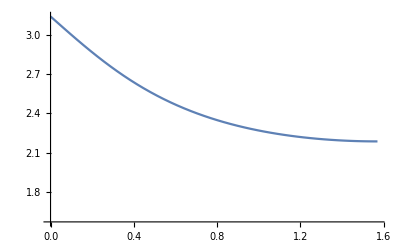

```mathematica
Plot[1. ArcCos[-(3.43283315962327*^15)/(√(1.1784343501809084*^31+2.3568697813555603*^31 Sin[t[1,3]]^2))],{t[1,3],0,Pi/2},PlotRange->{Pi/2,Pi}]
```

```mathematica
r03[t,11]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (Cos[t[3,3]] (-Cos[t[1,1]] Cos[t[2,2]] Sin[t[1,2]]+Sin[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]-(-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,1]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,1]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,1]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,1]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,1]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,1]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (Cos[t[3,3]] (-Cos[t[2,2]] Sin[t[1,1]] Sin[t[1,2]]-Cos[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,1]] Sin[t[1,3]]-(Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,1]] Sin[t[1,4]]-(Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,1]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,1]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,1]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,1]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,1]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,1]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,1]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,1]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,1]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,1]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,1]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,1]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,1]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,1]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,1]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,1]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,1]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,2]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,2]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,2]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,2]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,2]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[3,4]] (Cos[t[1,2]] Cos[t[2,2]] Cos[t[3,3]]+(-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,2]] Sin[t[2,3]]) Sin[t[3,3]])+(-Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,2]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,2]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,2]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,2]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,2]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,2]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,2]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,2]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,2]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,2]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,2]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,2]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,3]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,3]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,3]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,3]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[3,5]] (Cos[t[1,3]] Cos[t[2,3]] Cos[t[3,4]] Sin[t[3,3]]+(-Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]]) Sin[t[3,4]])+(-Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,3]] Sin[t[1,6]]-(Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,3]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,3]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,3]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,3]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,3]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,3]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,3]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,4]] Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,3]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,4]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,4]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,4]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,4]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[3,6]] (Cos[t[1,4]] Cos[t[2,4]] Cos[t[3,5]] Sin[t[3,4]]+(-Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]) Sin[t[3,5]])+(-Cos[t[1,5]] Cos[t[2,6]] Sin[t[1,4]] Sin[t[1,6]]-(Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]]) Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,4]] Sin[t[1,7]]-(Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,4]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,4]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,4]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,4]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[2,6]] (Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]])-Cos[t[1,5]] Sin[t[1,4]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,5]] Cos[t[1,6]] Sin[t[1,4]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,4]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,5]] Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,4]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,5]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,5]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,5]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,5]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[3,7]] (Cos[t[1,5]] Cos[t[2,5]] Cos[t[3,6]] Sin[t[3,5]]+(-Cos[t[2,6]] Sin[t[1,5]] Sin[t[1,6]]-Cos[t[1,5]] Sin[t[2,5]] Sin[t[2,6]]) Sin[t[3,6]])+(-Cos[t[1,6]] Cos[t[2,7]] Sin[t[1,5]] Sin[t[1,7]]-(Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]]) Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,6]] Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,5]] Sin[t[1,8]]-(Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,5]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,5]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,5]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[2,7]] (Cos[t[1,5]] Cos[t[2,6]] Sin[t[2,5]]-Sin[t[1,5]] Sin[t[1,6]] Sin[t[2,6]])-Cos[t[1,6]] Sin[t[1,5]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,6]] Cos[t[1,7]] Sin[t[1,5]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,6]] Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,5]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,6]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,7]] Sin[t[1,6]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,6]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,6]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[3,8]] (Cos[t[1,6]] Cos[t[2,6]] Cos[t[3,7]] Sin[t[3,6]]+(-Cos[t[2,7]] Sin[t[1,6]] Sin[t[1,7]]-Cos[t[1,6]] Sin[t[2,6]] Sin[t[2,7]]) Sin[t[3,7]])+(-Cos[t[1,7]] Cos[t[2,8]] Sin[t[1,6]] Sin[t[1,8]]-(Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]]) Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,7]] Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,6]] Sin[t[1,9]]-(Cos[t[2,8]] (Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,7]] Sin[t[1,6]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,7]] Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,6]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[2,8]] (Cos[t[1,6]] Cos[t[2,7]] Sin[t[2,6]]-Sin[t[1,6]] Sin[t[1,7]] Sin[t[2,7]])-Cos[t[1,7]] Sin[t[1,6]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,7]] Cos[t[1,8]] Sin[t[1,6]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,8]] Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,7]] | Cos[t[2,10]] (Cos[t[2,9]] (Cos[t[1,7]] Cos[t[2,8]] Sin[t[2,7]]-Sin[t[1,7]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,8]] Sin[t[1,7]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,8]] Cos[t[1,9]] Sin[t[1,7]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[3,9]] (Cos[t[1,7]] Cos[t[2,7]] Cos[t[3,8]] Sin[t[3,7]]+(-Cos[t[2,8]] Sin[t[1,7]] Sin[t[1,8]]-Cos[t[1,7]] Sin[t[2,7]] Sin[t[2,8]]) Sin[t[3,8]])+(-Cos[t[1,8]] Cos[t[2,9]] Sin[t[1,7]] Sin[t[1,9]]-(Cos[t[1,7]] Cos[t[2,8]] Sin[t[2,7]]-Sin[t[1,7]] Sin[t[1,8]] Sin[t[2,8]]) Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,8]] Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,7]] Sin[t[1,10]]-(Cos[t[2,9]] (Cos[t[1,7]] Cos[t[2,8]] Sin[t[2,7]]-Sin[t[1,7]] Sin[t[1,8]] Sin[t[2,8]])-Cos[t[1,8]] Sin[t[1,7]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,9]] Cos[t[1,10]] Sin[t[1,8]] | Cos[t[2,10]] (Cos[t[1,8]] Cos[t[2,9]] Sin[t[2,8]]-Sin[t[1,8]] Sin[t[1,9]] Sin[t[2,9]])-Cos[t[1,9]] Sin[t[1,8]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[3,10]] (Cos[t[1,8]] Cos[t[2,8]] Cos[t[3,9]] Sin[t[3,8]]+(-Cos[t[2,9]] Sin[t[1,8]] Sin[t[1,9]]-Cos[t[1,8]] Sin[t[2,8]] Sin[t[2,9]]) Sin[t[3,9]])+(-Cos[t[1,9]] Cos[t[2,10]] Sin[t[1,8]] Sin[t[1,10]]-(Cos[t[1,8]] Cos[t[2,9]] Sin[t[2,8]]-Sin[t[1,8]] Sin[t[1,9]] Sin[t[2,9]]) Sin[t[2,10]]) Sin[t[3,10]]
Cos[t[1,10]] Sin[t[1,9]] | Cos[t[1,9]] Cos[t[2,10]] Sin[t[2,9]]-Sin[t[1,9]] Sin[t[1,10]] Sin[t[2,10]] | Cos[t[1,9]] Cos[t[2,9]] Cos[t[3,10]] Sin[t[3,9]]+(-Cos[t[2,10]] Sin[t[1,9]] Sin[t[1,10]]-Cos[t[1,9]] Sin[t[2,9]] Sin[t[2,10]]) Sin[t[3,10]]
Sin[t[1,10]] | Cos[t[1,10]] Sin[t[2,10]] | Cos[t[1,10]] Cos[t[2,10]] Sin[t[3,10]])

```mathematica
((r03[t,11])/.{
t[1,10]->0,t[1,9]->0,t[1,8]->0,t[1,7]->0,t[1,6]->0,t[1,5]->0,t[1,4]->0,
t[2,10]->0,t[2,9]->0,t[2,8]->0,t[2,3]->0,t[2,2]->0,t[2,4]->Pi/2,
t[3,7]->0,t[3,6]->0,t[3,3]->0,t[3,4]->Pi/2})//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] | 0 | Cos[t[3,5]] Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] Sin[t[1,1]]
Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] | 0 | -Cos[t[1,1]] Cos[t[3,5]] Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]]
Cos[t[1,3]] Sin[t[1,2]] | 0 | 0
Sin[t[1,3]] | 0 | 0
0 | Cos[t[2,5]] Cos[t[2,6]] Cos[t[2,7]] | -Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] Sin[t[2,5]] Sin[t[3,5]]
0 | Cos[t[2,6]] Cos[t[2,7]] Sin[t[2,5]] | Cos[t[2,5]] Cos[t[3,8]] Cos[t[3,9]] Cos[t[3,10]] Sin[t[3,5]]
0 | Cos[t[2,7]] Sin[t[2,6]] | 0
0 | Sin[t[2,7]] | 0
0 | 0 | Cos[t[3,9]] Cos[t[3,10]] Sin[t[3,8]]
0 | 0 | Cos[t[3,10]] Sin[t[3,9]]
0 | 0 | Sin[t[3,10]])

```mathematica
r04[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
Do[mat=mat.rota[t[2,i-1],n,2,i],{i,3,n}];
Do[mat=mat.rota[t[3,i-1],n,3,i],{i,4,n}];
Do[mat=mat.rota[t[4,i-1],n,4,i],{i,5,n}];
mat[[;;,1;;4]]]
```

```mathematica
((r04[t,11])/.{
t[1,10]->0,t[1,9]->0,t[1,8]->0,t[1,7]->0,t[1,6]->0,t[1,5]->0,t[1,4]->0,t[1,3]->0,
t[2,10]->0,t[2,9]->0,t[2,8]->0,t[2,7]->0,t[2,6]->0,t[2,2]->0,t[2,3]->Pi/2,
t[3,10]->0,t[3,9]->0,t[3,5]->0,t[3,4]->0,t[3,6]->Pi/2
})//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] | 0 | 0 | Cos[t[4,7]] Cos[t[4,8]] Cos[t[4,9]] Cos[t[4,10]] (Cos[t[4,4]] Cos[t[4,5]] Cos[t[4,6]] (Cos[t[3,3]] Sin[t[1,1]]+Cos[t[1,1]] Sin[t[1,2]] Sin[t[3,3]])+(Cos[t[1,1]] Cos[t[3,3]] Sin[t[1,2]]-Sin[t[1,1]] Sin[t[3,3]]) Sin[t[4,6]])
Cos[t[1,2]] Sin[t[1,1]] | 0 | 0 | Cos[t[4,7]] Cos[t[4,8]] Cos[t[4,9]] Cos[t[4,10]] (Cos[t[4,4]] Cos[t[4,5]] Cos[t[4,6]] (-Cos[t[1,1]] Cos[t[3,3]]+Sin[t[1,1]] Sin[t[1,2]] Sin[t[3,3]])+(Cos[t[3,3]] Sin[t[1,1]] Sin[t[1,2]]+Cos[t[1,1]] Sin[t[3,3]]) Sin[t[4,6]])
Sin[t[1,2]] | 0 | 0 | Cos[t[4,7]] Cos[t[4,8]] Cos[t[4,9]] Cos[t[4,10]] (-Cos[t[1,2]] Cos[t[4,4]] Cos[t[4,5]] Cos[t[4,6]] Sin[t[3,3]]-Cos[t[1,2]] Cos[t[3,3]] Sin[t[4,6]])
0 | Cos[t[2,4]] Cos[t[2,5]] | 0 | Cos[t[4,6]] Cos[t[4,7]] Cos[t[4,8]] Cos[t[4,9]] Cos[t[4,10]] (-Cos[t[4,5]] Sin[t[2,4]] Sin[t[4,4]]-Cos[t[2,4]] Sin[t[2,5]] Sin[t[4,5]])
0 | Cos[t[2,5]] Sin[t[2,4]] | 0 | Cos[t[4,6]] Cos[t[4,7]] Cos[t[4,8]] Cos[t[4,9]] Cos[t[4,10]] (Cos[t[2,4]] Cos[t[4,5]] Sin[t[4,4]]-Sin[t[2,4]] Sin[t[2,5]] Sin[t[4,5]])
0 | Sin[t[2,5]] | 0 | Cos[t[2,5]] Cos[t[4,6]] Cos[t[4,7]] Cos[t[4,8]] Cos[t[4,9]] Cos[t[4,10]] Sin[t[4,5]]
0 | 0 | Cos[t[3,7]] Cos[t[3,8]] | Cos[t[4,9]] Cos[t[4,10]] (-Cos[t[4,8]] Sin[t[3,7]] Sin[t[4,7]]-Cos[t[3,7]] Sin[t[3,8]] Sin[t[4,8]])
0 | 0 | Cos[t[3,8]] Sin[t[3,7]] | Cos[t[4,9]] Cos[t[4,10]] (Cos[t[3,7]] Cos[t[4,8]] Sin[t[4,7]]-Sin[t[3,7]] Sin[t[3,8]] Sin[t[4,8]])
0 | 0 | Sin[t[3,8]] | Cos[t[3,8]] Cos[t[4,9]] Cos[t[4,10]] Sin[t[4,8]]
0 | 0 | 0 | Cos[t[4,10]] Sin[t[4,9]]
0 | 0 | 0 | Sin[t[4,10]])